```mathematica
data={{1,0,0},{2,1,0},{3,1,1}}
```

{{1,0,0},{2,1,0},{3,1,1}}

18

16

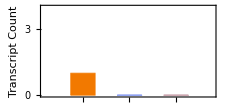

```mathematica
fontS=18
fontS0=16
Show[BarChart[data[[1]],BaseStyle->{"Helvetica",12,Black},AspectRatio->1/(1.3*GoldenRatio), FrameTicks->{{Range[0,4,1],None},{Automatic,None}},ChartStyle->{Darker[Orange,0.05],ColorData["ThermometerColors"][0.15],ColorData[24][8]},ChartLabels->{{"Interphase","M-phase"(*,"cell cycle 2","cell cycle 3","cell cycle 4"*)(*,"",""*)},{Style["gene^1",Black,Italic,fontS0],Style["gene^2",Black,Italic,fontS0],Style["gene^3",Black,Italic,fontS0]}},Frame->True,(*ImagePadding->{{All,All},{All,All}},*)(*PlotLabel->Style["Expected Gene Distrbution, Without Parental Transfer",Black,15,Bold],*)FrameLabel->{{Style["Transcript Count",Black,fontS],None},{"",Style["  ",fontS,Bold]}},ImageSize->225,BarSpacing->{0.9,1.5},ChartLayout->"Grouped",BarOrigin->Bottom,FrameStyle->{Black,Thickness[0.002]}],PlotRange->{All,{0,4}},BaseStyle->{"Helvetica",16,Black}]
```

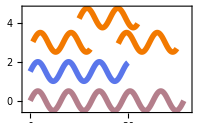

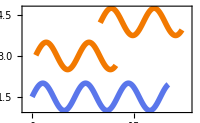

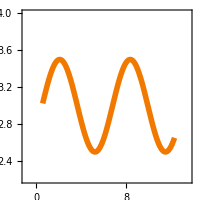

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
fn[x_]:=.5Sin[x]
Plot[{If[x>12.3||x<0.55,Null,fn[x-0.5]+3],If[x<10||x>22,Null,fn[x+2.5]+4.25],
If[x<18||x>30,Null,fn[x+7]+3.],
If[x>20,Null,fn[x]+1.5],fn[x]},{x,0,10Pi},Frame->True,FrameTicks->{None,None},FrameStyle->Directive[Gray,Dashed],Axes->False,PlotStyle->{Directive[Thickness[0.02],Darker[Orange,0.05]],
Directive[Thickness[0.02],Darker[Orange,0.05]],
Directive[Thickness[0.02],Darker[Orange,0.05]],Directive[Thickness[0.02],ColorData["ThermometerColors"][0.15]],Directive[Thickness[0.02],ColorData[24][8]]},PlotRange->{{-1,10Pi+1},All},ImageSize->200]
Plot[{If[x>12.3||x<0.55,Null,fn[x-0.5]+3],If[x<10||x>22,Null,fn[x+2.5]+4.25],
(*If[x<18||x>30,Null,fn[x+7]+3.],*)
If[x>20,Null,fn[x]+1.5](*,fn[x]+2*)},{x,0,10Pi},Frame->True,FrameTicks->{None,None},FrameStyle->Directive[Gray,Dashed],Axes->False,PlotStyle->{Directive[Thickness[0.02],Darker[Orange,0.05]],
Directive[Thickness[0.02],Darker[Orange,0.05]],
(*Directive[Thickness[0.02],White],*)Directive[Thickness[0.02],ColorData["ThermometerColors"][0.15]],Directive[Thickness[0.02],White]},PlotRange->{{-1,7Pi+1},All},ImageSize->200]
Plot[If[x>12.3||x<0.55,Null,fn[x-0.5]+3](*,If[x<10||x>22,Null,fn[x+2.5]+4.25],*)
(*If[x<18||x>30,Null,fn[x+7]+3.],*)
(*If[x>20,Null,fn[x]+1.5]*)(*,fn[x]+2*),{x,0,5Pi},Frame->True,FrameTicks->{None,None},FrameStyle->Directive[Gray,Dashed],Axes->False,PlotStyle->{Directive[Thickness[0.02],Darker[Orange,0.05]]
(*Directive[Thickness[0.02],White],*)(*Directive[Thickness[0.02],ColorData["ThermometerColors"][0.15]],Directive[Thickness[0.02],White]*)},PlotRange->{{-1,4Pi+1},{2.2,4}},ImageSize->200,AspectRatio->Automatic]
Plot[{If[x>12.3||x<0.55,Null,fn[x-0.5]+3],If[x<10||x>22,Null,fn[x+2.5]+4.25],
If[x<18||x>30,Null,fn[x+7]+3.],
If[x>20,Null,fn[x]+1.5],fn[x]},{x,0,10Pi},Frame->True,FrameTicks->{None,None},FrameStyle->Directive[Gray,Dashed],Axes->False,PlotStyle->{Directive[Thickness[0.02],Darker[Orange,0.05]],
Directive[Thickness[0.02],Darker[Orange,0.05]],
Directive[Thickness[0.02],Darker[Orange,0.05]],Directive[Thickness[0.02],ColorData["ThermometerColors"][0.15]],Directive[Thickness[0.02],ColorData[24][8]]},PlotRange->{{-1,10Pi+1},All},ImageSize->200]
Plot[{
If[x>20,Null,fn[x]+1.5]},{x,0,10Pi},Frame->False,FrameTicks->{None,None},FrameStyle->Directive[Gray,Dashed],Axes->False,PlotStyle->{Directive[Thickness[0.02],ColorData["ThermometerColors"][0.15]]},PlotRange->{{-1,7Pi+1},{1,2}},ImageSize->100]

Plot[{fn[x]},{x,0,10Pi},Frame->False,FrameTicks->{None,None},FrameStyle->Directive[Gray,Dashed],Axes->False,PlotStyle->{Directive[Thickness[0.02],ColorData[24][8]]},PlotRange->{{-1,10Pi+1},{-1,1}},ImageSize->100]
Plot[{If[x>12.3||x<0.55,Null,fn[x-0.5]+3]},{x,0,10Pi},Frame->False,FrameTicks->{None,None},FrameStyle->Directive[Gray,Dashed],Axes->False,PlotStyle->{Directive[Thickness[0.02],Darker[Orange,0.05]]},PlotRange->{{-1,5Pi+1},{2,4}},ImageSize->100
]
```